# Analysis of Triangle Completion Categorical experiment

## Loading the data and functions

```mathematica
SetDirectory["/home/uvhart/GitHubLib/EuclideanGeoSurvey"];
```

```mathematica
SetDirectory["/Users/alcarden4/Desktop/WebstormProjects/EuclideanGeoSurvey"]
```

```mathematica
Needs["ErrorBarPlots`"];
LogFilePilot1=DeleteCases[Import["logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFileExp1=DeleteCases[Import["logVertexCatExp.txt","Table"],Except[{___,"ERROR",___}]];
```

```mathematica
LogFilePilot1;
```

#### Data

```mathematica
DataUnCln={LogFileExp1[[;;,;;2]],LogFileExp1[[;;,6;;]]}ᵀ;
DATA=Join[#[[1]],If[Length[#[[2]]]==1,StringSplit[#[[2,1]],"_"],Join[StringSplit[#[[2,1]],"_"],#[[2,2;;]]]]]&/@DataUnCln;
DATASort=Select[Select[GatherBy[DATA,#[[3]]&],Length@#>127&],#[[5,5]]≠"9999"&];
DataClean={Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},SortBy[#,#[[{1,2}]]&]&@GatherBy[Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]],#[[{1,2}]]&]}&/@DATASort;
(*ID,gender,age,right/left handed,education*)
(*7=angle; 9=base factor; 11=Qtype; 12=Manipulation; 13=What's manipulated; 15=correct answer; 17=timing; 19=user answer;*)
DataClnGraded=Join@@@Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataClean[[;;,2]],{3}];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

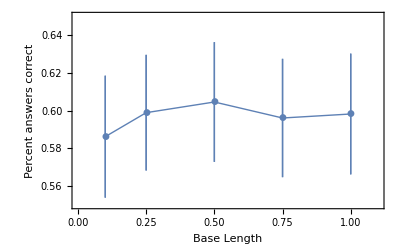

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0.55,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Angle Size

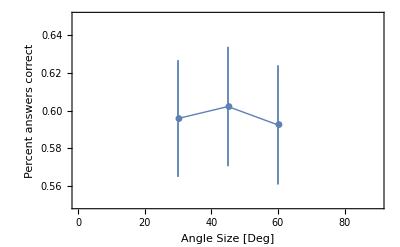

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0.55,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

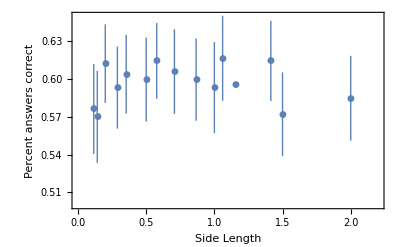

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.5,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Mean@#[[;;,-1]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (people get better vertex location than angle estimations)

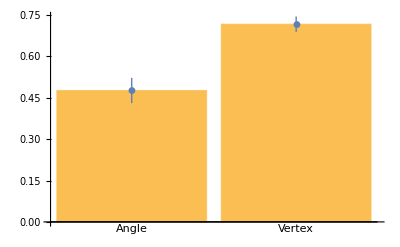

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3}]]&]&/@DataClnGraded,{2}],First])]
```

#### What’s being manipulated (angle manipulation than distance manipulations)

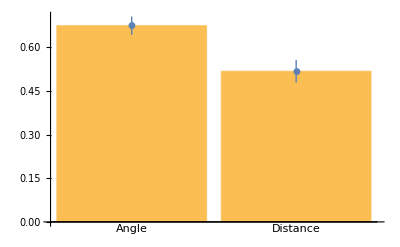

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{5}]]&]&/@DataClnGraded,{2}],First])],First]
```

#### What’s being manipulated (no difference for increase/decrease)

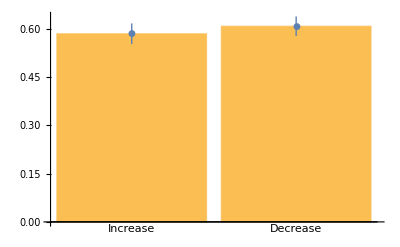

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="increase",1,2],#[[2]]}&,{#[[1,4]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{4}]]&]&/@DataClnGraded,{2}],First])],First]
```

#### Every Question Type Alone (easiest -> vertex and angle change, hardest->angles when distance changes)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

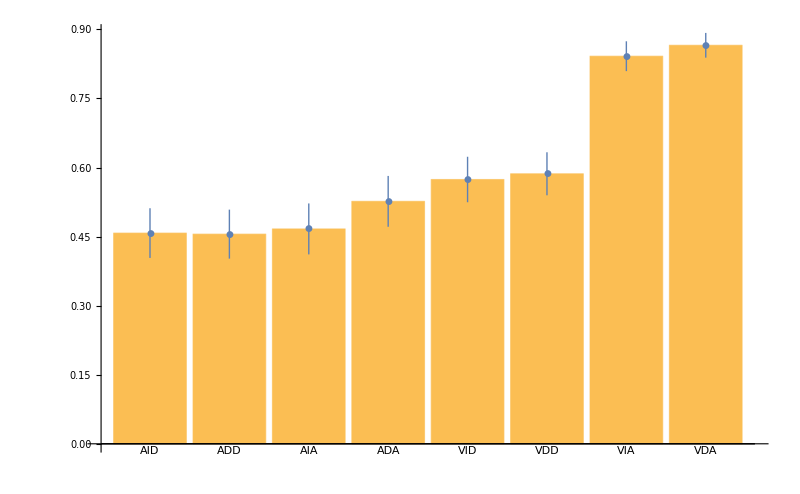

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@GatherBy[Join@@(({#[[1,{3,4,5}]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataClnGraded)/.rules),First]],First]
```

## Response times

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

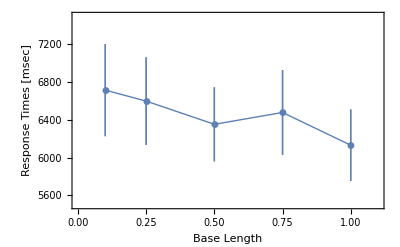

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{5500,7.5 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Response Times vs. Angle Size (no dependence on angle size)

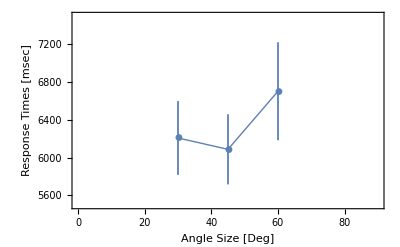

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{5.5 10^3,7.5 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

```mathematica
MannWhitneyTest[(Transpose[{#[[1,1]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])[[{1,3},;;,2]]]
```

0.666773

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

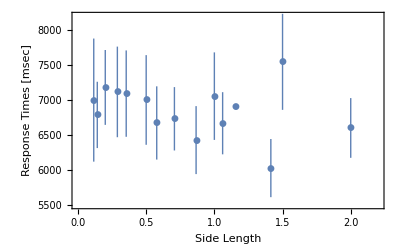

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{5.5 10^3,8.2 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Median@ToExpression@#[[;;,7]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

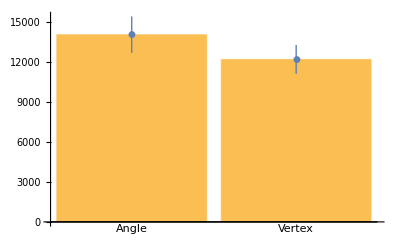

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Mean@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3}]]&]&/@DataClnGraded,{2}],First])]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3}]]&]&/@DataClnGraded,{2}],First])[[;;,;;,2]]
```

0.454379

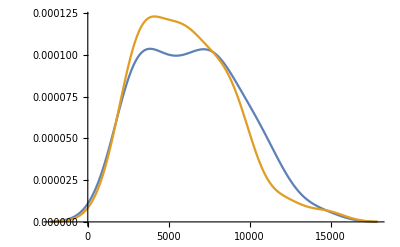

```mathematica
SmoothHistogram@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3}]]&]&/@DataClnGraded,{2}],First])[[;;,;;,2]]
```

#### What’s being manipulated

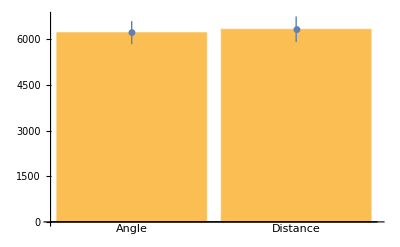

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{5}]]&]&/@DataClnGraded,{2}],First])],First]
```

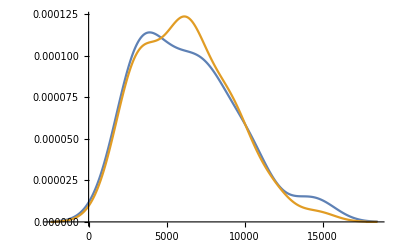

```mathematica
SmoothHistogram@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{5}]]&]&/@DataClnGraded,{2}],First])[[;;,;;,2]]
```

#### What’s the manipulation

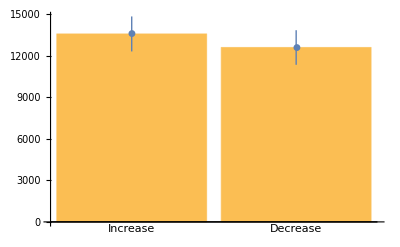

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="increase",1,2],#[[2]]}&,{#[[1,4]],Mean@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{4}]]&]&/@DataClnGraded,{2}],First])],First]
```

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

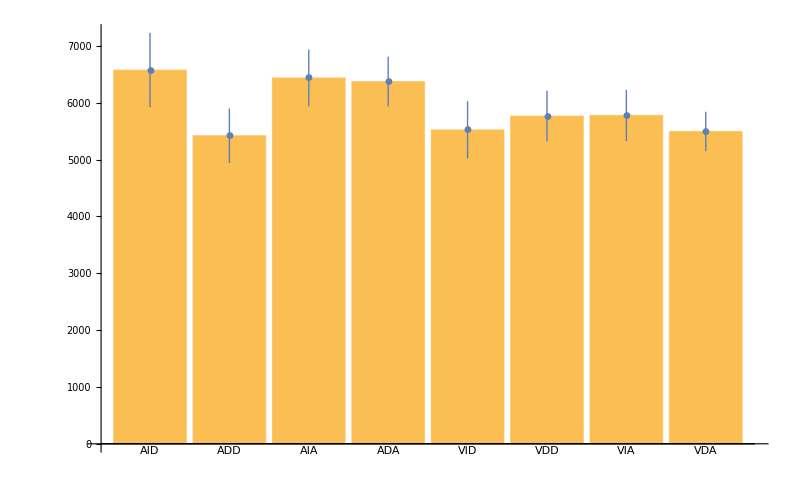

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@GatherBy[Join@@(({#[[1,{3,4,5}]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataClnGraded)/.rules),First]],First]
```

```mathematica
MannWhitneyTest@(SortBy[GatherBy[Join@@(({#[[1,{3,4,5}]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataClnGraded)/.rules),First],First][[{1,2},;;,2]])
```

0.480762

## Learning effect

```mathematica
DataCleanFirst40=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#[[;;46]],StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanLast40=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#[[-44;;]],StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanAll=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
```

```mathematica
DataCleanFirst40Graded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanFirst40[[;;,2]],{2}];
DataCleanLast40Graded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanLast40[[;;,2]],{2}];
DataCleanAllGraded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanAll[[;;,2]],{2}];
```

### Change in response times (first 40 vs. last 40)

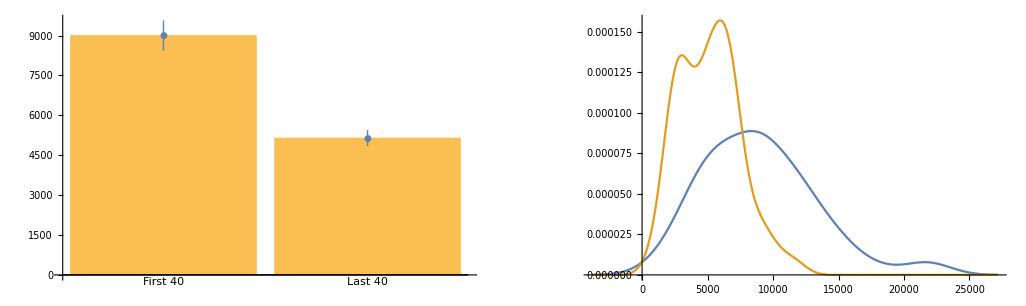

```mathematica
GraphicsRow@{Show[BarChart[#[[;;,1]],ChartLabels->{"First 40","Last 40"}],ErrorListPlot[#,PlotStyle->Thick,PlotMarkers->Automatic]]&@(N@{Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&/@{Median/@ToExpression@DataCleanFirst40Graded[[;;,;;,7]],Median/@ToExpression@DataCleanLast40Graded[[;;,;;,7]]}),SmoothHistogram@{Median/@ToExpression@DataCleanFirst40Graded[[;;,;;,7]],Median/@ToExpression@DataCleanLast40Graded[[;;,;;,7]]}}
```

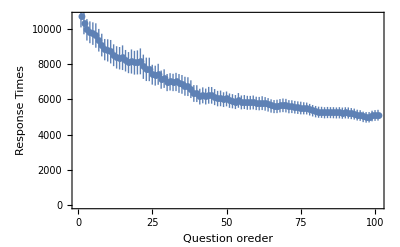

```mathematica
ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"Question oreder","Response Times"},PlotStyle->Thick,PlotMarkers->Automatic]&@(N@({Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&@(Median/@Partition[#,20,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]])))ᵀ)
```

```mathematica
Manipulate[ListPlot[#[[i]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Question order","Response Time [ms]"}]&@(N@(Median/@Partition[#,20,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]]))),{i,1,Length@DataCleanAllGraded,1}]
```

### Change in percent correct (first 40 vs. last 40)

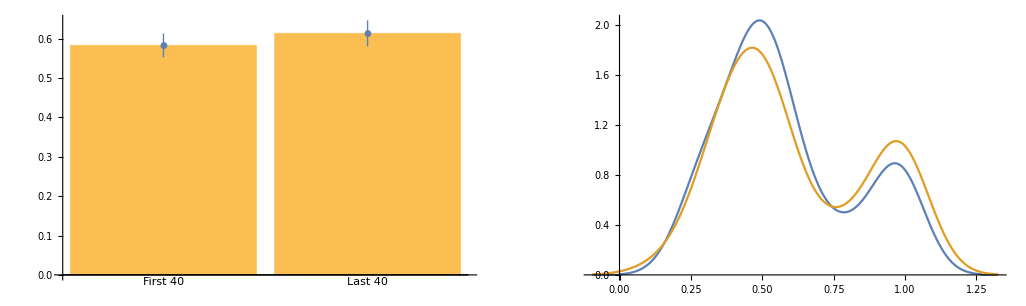

```mathematica
GraphicsRow@{Show[BarChart[#[[;;,1]],ChartLabels->{"First 40","Last 40"}],ErrorListPlot[#,PlotStyle->Thick,PlotMarkers->Automatic]]&@(N@{Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&/@{Mean/@ToExpression@DataCleanFirst40Graded[[;;,;;,-1]],Mean/@ToExpression@DataCleanLast40Graded[[;;,;;,-1]]}),SmoothHistogram@{Mean/@ToExpression@DataCleanFirst40Graded[[;;,;;,-1]],Mean/@ToExpression@DataCleanLast40Graded[[;;,;;,-1]]}}
```

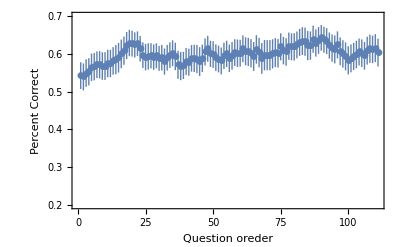

```mathematica
ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"Question oreder","Percent Correct"},PlotStyle->Thick,PlotMarkers->Automatic,PlotRange->{All,{0.2,0.7}}]&@(N@({Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&@(Mean/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,-1]])))ᵀ)
```

```mathematica
Manipulate[,{i,1,Length@DataCleanAllGraded,1}]
```

```mathematica
Manipulate[GraphicsRow[{ListPlot[#[[i]],Joined->True,PlotRange->{All,{0,1}},Frame->True,FrameLabel->{"Question order","Percent Correct"}]&@(N@(Mean/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,-1]]))),ListPlot[#[[i]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Question order","Response Time [ms]"}]&@(N@(Median/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]])))},ImageSize->800],{i,1,Length@DataCleanAllGraded,1}]
```

First 40 questions analysis

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

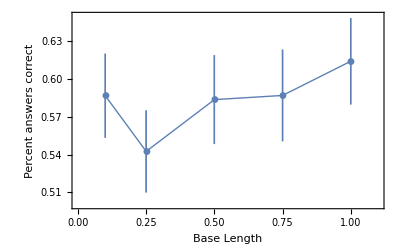

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0.5,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{2}]]&]&/@DataCleanFirst40Graded,{2,1,3}])
```

### Percent correct vs. Angle Size

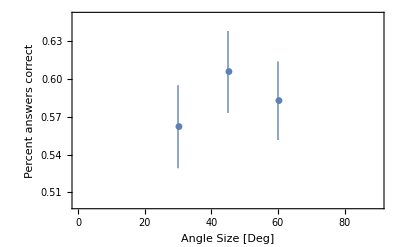

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.5,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{1}]]&]&/@DataCleanFirst40Graded,{2,1,3}])
```

### Percent correct vs. Side length (wrong)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

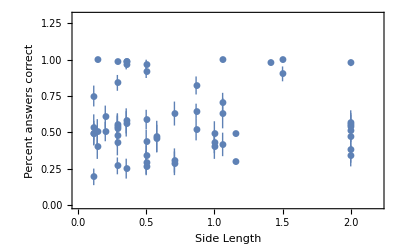

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,1.3}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Mean@#[[;;,-1]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataCleanFirst40Graded),{2}])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

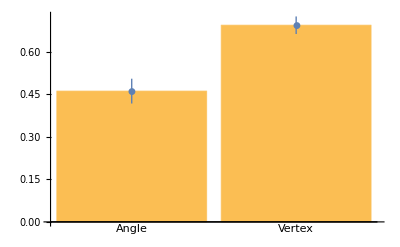

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

#### What’s being manipulated

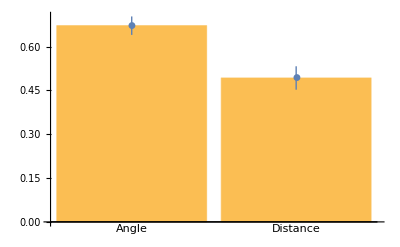

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{5}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

#### What’s being manipulated

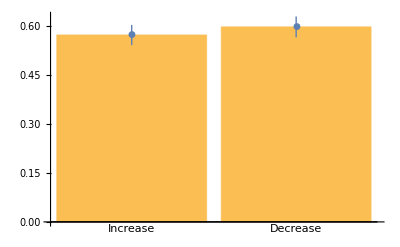

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="increase",1,2],#[[2]]}&,{#[[1,4]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{4}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

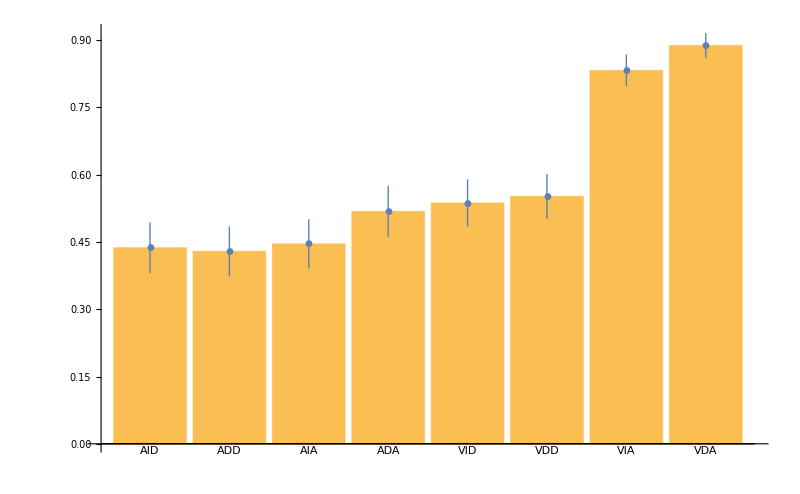

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@GatherBy[Join@@(({#[[1,{3,4,5}]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataCleanFirst40Graded)/.rules),First]],First]
```

## Response times

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

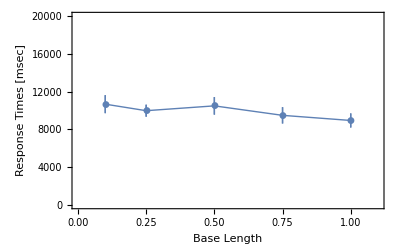

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{2}]]&]&/@DataCleanFirst40Graded,{2,1,3}])
```

### Response Times vs. Angle Size

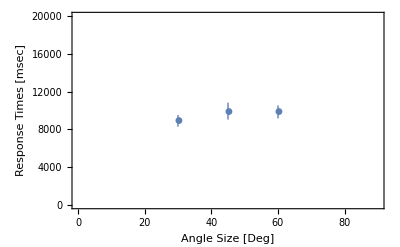

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0,20 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{1}]]&]&/@DataCleanFirst40Graded,{2,1,3}])
```

### Response Time vs. Side length (wrong)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,20 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Median@ToExpression@#[[;;,7]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataCleanFirst40Graded),{2}],{2,1,3}])
```

Transpose::tperm: Permutation {2,1,3} is longer than the dimensions {59} of the expression.

Part::partd: Part specification {2,1,3}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {2,1,3}⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::tperm: Permutation {{{2,1,3}⟦1,1⟧,Mean[{2,1,3}⟦1;;All,2⟧]},ErrorBar[0.57735 StandardDeviation[{2.,1.,3.}⟦1;;All,2⟧]]} is longer than the dimensions {2} of the expression.

General::stop: Further output of Transpose::tperm will be suppressed during this calculation.

Transpose::perm1: Entry {2,1,3}⟦1,1⟧ in permutation {{2,1,3}⟦1,1⟧,Mean[{2,1,3}⟦1;;All,2⟧]} is not a positive machine integer.

Transpose::perm1: Entry {2.,1.,3.}⟦1,1⟧ in permutation {{2.,1.,3.}⟦1,1⟧,Mean[{2.,1.,3.}⟦1;;All,2⟧]} is not a positive machine integer.

General::stop: Further output of Transpose::perm1 will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{1.,0.2,8694.5},{2.,0.770794,13876.6}},{{2.,1.,3.}⟦1,1⟧,Mean[{2.,1.,3.}⟦1;;All,2⟧]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[{{1,0.2,17389/2},{2,0.770794,1637437/118}},{{2,1,3}⟦1,1⟧,Mean[{2,1,3}⟦1;;All,2⟧]}],{PlotRange→{{0,2.2},{0,20000}},Frame→{True,True,False,False},FrameLabel→{Side Length,Response Times [msec]},PlotStyle→Thickness[Large],PlotMarkers→Automatic},Method→{OptimizePlotMarkers→False}]

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

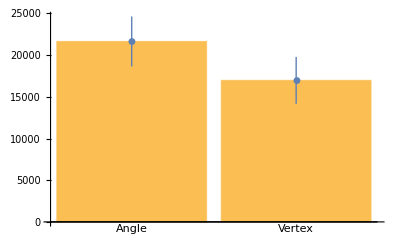

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Mean@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

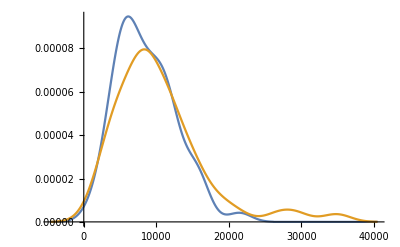

```mathematica
SmoothHistogram@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3}]]&]&/@DataCleanFirst40Graded,{2}],First])[[;;,;;,2]]
```

#### What’s being manipulated

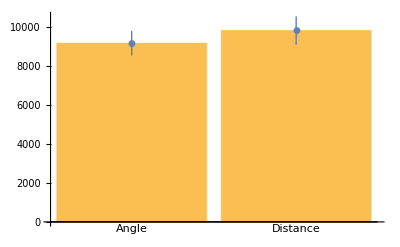

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{5}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

```mathematica
SmoothHistogram@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{5}]]&]&/@DataClnGraded,{2}],First])[[;;,;;,2]]
```

-Graphics-

#### What’s being manipulated

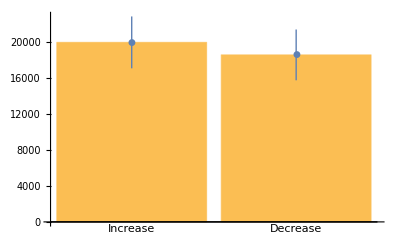

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="increase",1,2],#[[2]]}&,{#[[1,4]],Mean@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{4}]]&]&/@DataCleanFirst40Graded,{2}],First])],First]
```

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

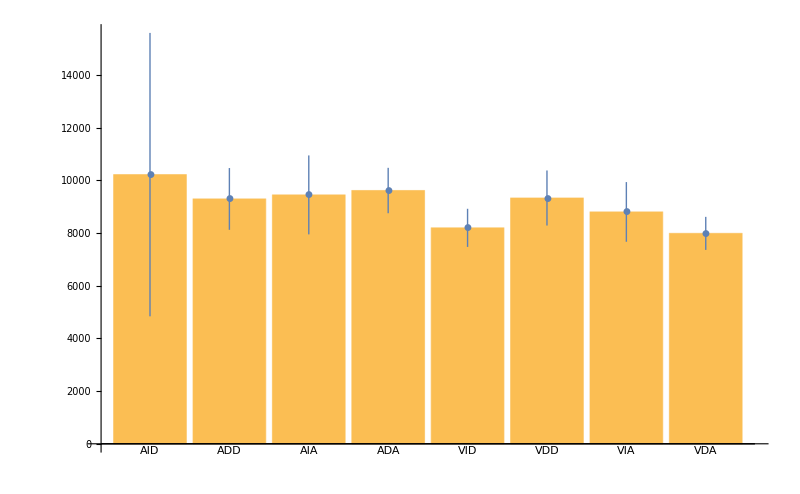

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@GatherBy[Join@@(({#[[1,{3,4,5}]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataCleanFirst40Graded)/.rules),First]],First]
```